```mathematica
ClearAll["Global`*"]
$Assumptions[Element[t,Reals],Element[ϵ,Reals],Element[s,Reals]]
$Assumptions[Element[x[t],Reals],Element[y[t],Reals],Element[z[t],Reals],Element[w[t],Reals]]
system={x''[t]==z'[t]*w[t]-y'[t]*a,
y''[t]==x'[t]*a-z'[t]*b,
z''[t]==y'[t]*b-x'[t]*w[t],
w'[t]==ϵ}
```

True[t∈ℝ,ϵ∈ℝ,s∈ℝ]

True[x[t]∈ℝ,y[t]∈ℝ,z[t]∈ℝ,w[t]∈ℝ]

{x''[t]==-a y'[t]+w[t] z'[t],y''[t]==a x'[t]-b z'[t],z''[t]==-w[t] x'[t]+b y'[t],w'[t]==ϵ}

```mathematica
initialv={x'[0]==0,y'[0]==0,z'[0]==s}
initial={x[0]==0,y[0]==0,z[0]==0,w[0]==W}
```

{x'[0]==0,y'[0]==0,z'[0]==s}

{x[0]==0,y[0]==0,z[0]==0,w[0]==W}

```mathematica
equations = Join[system, initialv, initial]
res = DSolve[equations, {x,y,z,w},t]
```

{x''[t]==-a y'[t]+w[t] z'[t],y''[t]==a x'[t]-b z'[t],z''[t]==-w[t] x'[t]+b y'[t],w'[t]==ϵ,x'[0]==0,y'[0]==0,z'[0]==s,x[0]==0,y[0]==0,z[0]==0,w[0]==W}

```mathematica
sx[t_]=D[x[t]/.res[[1]],t]
sy[t_]=D[y[t]/.res[[1]],t]
sz[t_]=D[z[t]/.res[[1]],t]
```

-s Sin[(t^2 ϵ)/2]

s Cos[(t^2 ϵ)/2]

```mathematica
xr[t_]:=Evaluate[x[t]/.res[[1]]]
yr[t_]:=Evaluate[y[t]/.res[[1]]]
zr[t_]:=Evaluate[z[t]/.res[[1]]]
$Assumptions[Element[xr[t],Reals],Element[yr[t],Reals],Element[zr[t],Reals],Element[sx[t],Reals],Element[sy[t],Reals],Element[zr[t],Reals]]
```

Element::bset: The second argument Real of Element should be one of: Primes, Integers, Rationals, Algebraics, Reals, Complexes, or Booleans.

General::stop: Further output of Element::bset will be suppressed during this calculation.

True[-(√π s FresnelS[(t √ϵ)/(√π)])/(√ϵ)∈Real,(√π s FresnelC[(t √ϵ)/(√π)])/(√ϵ)∈Real,-s Sin[(t^2 ϵ)/2]∈Real,s Cos[(t^2 ϵ)/2]∈Real]

```mathematica
tangentLine=(Y-yr[t])==(sy[t]/sx[t]) (X-xr[t]);
tres=Solve[tangentLine, t]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve. Try Reduce or FindInstance instead.

Solve[Y-(√π s FresnelC[(t √ϵ)/(√π)])/(√ϵ)==-Cot[(t^2 ϵ)/2] (X+(√π s FresnelS[(t √ϵ)/(√π)])/(√ϵ)),t]

```mathematica
X=2
Y =8
ϵ=-0.1
s=2.0
tres=Solve[tangentLine, t]
```

2

8

-0.1

2.

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

Solve[8+(0.+11.21 ⅈ) FresnelC[(0.+0.178412 ⅈ) t]==Cot[0.05 t^2] (2-(0.+11.21 ⅈ) FresnelS[(0.+0.178412 ⅈ) t]),t]

```mathematica
t1=t/.tres[[1]]
```

3.11461

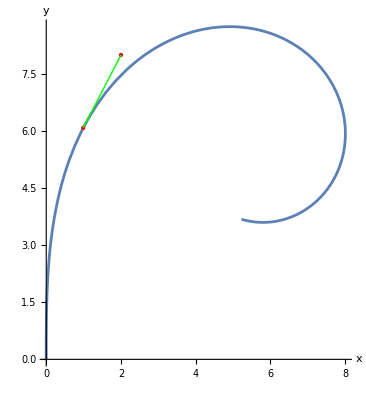

```mathematica
ParametricPlot[{xr[t],yr[t]},{t,0,10},AspectRatio->Automatic,AxesLabel->{"x","y"},
Epilog -> {
Red,PointSize[Large], Point[{xr[t1],yr[t1]}],
Red,PointSize[Large], Point[{X,Y}],
Green, Thick, Line[{{xr[t1],yr[t1]},{X,Y}}]
}]
```